```mathematica
D[ρ[r]*u[r],r] + ρ[r]*u[r]/r
D[ρ[r]*u[r]^2 + p[r],r] + ρ[r]*u[r]^2/r 
D[ρ[r]*u[r]^3 /2+ γ*u[r]*p[r]/(γ-1),r] + ρ[r]*u[r]^3/(2*r) +γ*u[r] p[r]/(γ-1)/r
```

(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]

(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]

(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]

```mathematica
Решаем
```

```mathematica
γ=2.0;
r1=0.17;
F=4;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[0.1]==1,ρ[0.1]==1,p[0.1]==0.05},{ρ,u,p},{r,0.1,r1}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

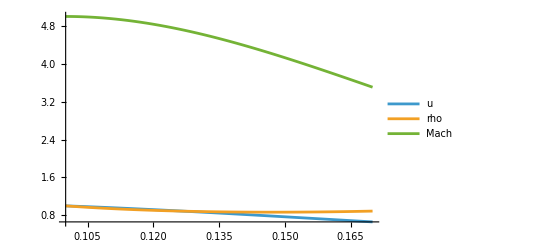

```mathematica
Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","Mach"}]
```

```mathematica
DD = 0;
ro1 =ρ[r1]/. s
p1 = p[r1]/. s
u1 = u[r1]/. s
g = 2.0;
ss = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 == ro*u*(u - DD)+ p&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals]
```

{0.889485}

{0.0395591}

{0.661322}

{{p→0.246155,ro→1.89687,u→0.310108},{p→0.0395591,ro→0.889485,u→0.661322}}

```mathematica
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
r2=0.8;
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[r1]==g1,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

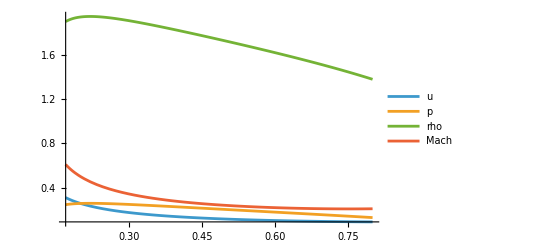

```mathematica
Plot[{Evaluate[u[r]/. sss],Evaluate[p[r]/. sss], Evaluate[ρ[r]/. sss], Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. sss]},{r,r1,r2},PlotRange->All,PlotLegends->{"u","p","rho","Mach"}]
```

```mathematica
xValues=Range[0.15,2,0.02]; (*шаг 0.1*)
pValues=p[xValues]/. sss;
Export["D:sss.csv",pValues,"CSV"];
```

```mathematica
yValues
```

{{0.329226,0.346277,0.354316,0.357772,0.358616,0.357876,0.356136,0.353751,0.350944,0.347863,0.344604,0.341235,0.337802,0.334339,0.330867,0.327404,0.32396,0.320544,0.31716,0.313814,0.310507,0.30724,0.304015,0.300831,0.297688,0.294585,0.291521,0.288497,0.285509,0.282558,0.279643,0.276761,0.273911,0.271094,0.268306,0.265548,0.262818,0.260114,0.257436,0.254783,0.252153,0.249545,0.24696,0.244394,0.241848,0.239321,0.236811,0.234318,0.231841,0.229379,0.226932,0.224498,0.222076,0.219667,0.217268,0.21488,0.212502,0.210132,0.207771,0.205417,0.20307,0.200729,0.198394,0.196063,0.193736,0.191413,0.189092,0.186773,0.184455,0.182137,0.179819,0.177501,0.17518,0.172857,0.17053,0.1682,0.165864,0.163523,0.161174,0.158818,0.156454,0.15408,0.151695,0.149298,0.146889,0.144465,0.142026,0.13957,0.137096,0.134602,0.132087,0.129548,0.126984}}

```mathematica
data=Transpose[xValues,yValues];
```